## Database Needs

```mathematica
PrependTo[$Path,NotebookDirectory[]];
```

```mathematica
<<DataProcessing`
```

```mathematica
Needs["DatabaseLink`"]
```

## Single Power Law

```mathematica
CloseSQLConnection /@ SQLConnections[];
db = "sim_v3_8_17_2017";
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/"<>db],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
res=getLogData[db,AxisRange->5000];
```

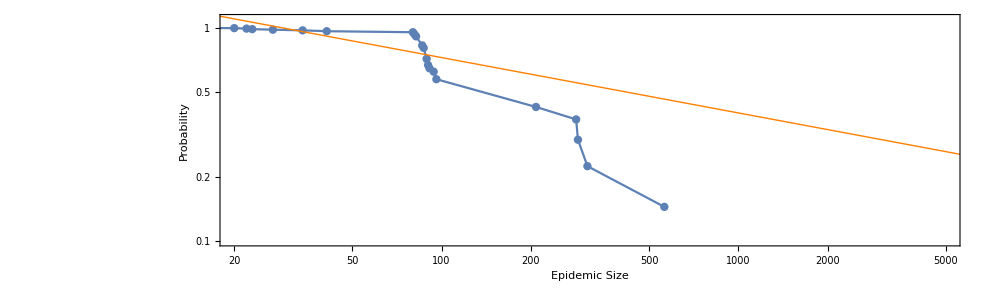

```mathematica
g=Show[{res["Log Probability Distribution"],res["Linear Model"]},ImageSize->{1000,Automatic}]
```

```mathematica
Export["/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/WithEcplise.jpg", g]
```

/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/WithEcplise.jpg

## History Data

### Connect to Database

```mathematica
CloseSQLConnection /@ SQLConnections[];
db = "sim_v3_1_9_2017";
```

CloseSQLConnection /@ SQLConnections[];
db = "sim_v2_8_17_2017";

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/"<>db],"Username"->"root","Password"->""]
```

SQLConnection[…]

### Extract data

```mathematica
HistoryData=SQLSelect[conn,"HistoryData"];
```

```mathematica
res:=getLogData[db]
```

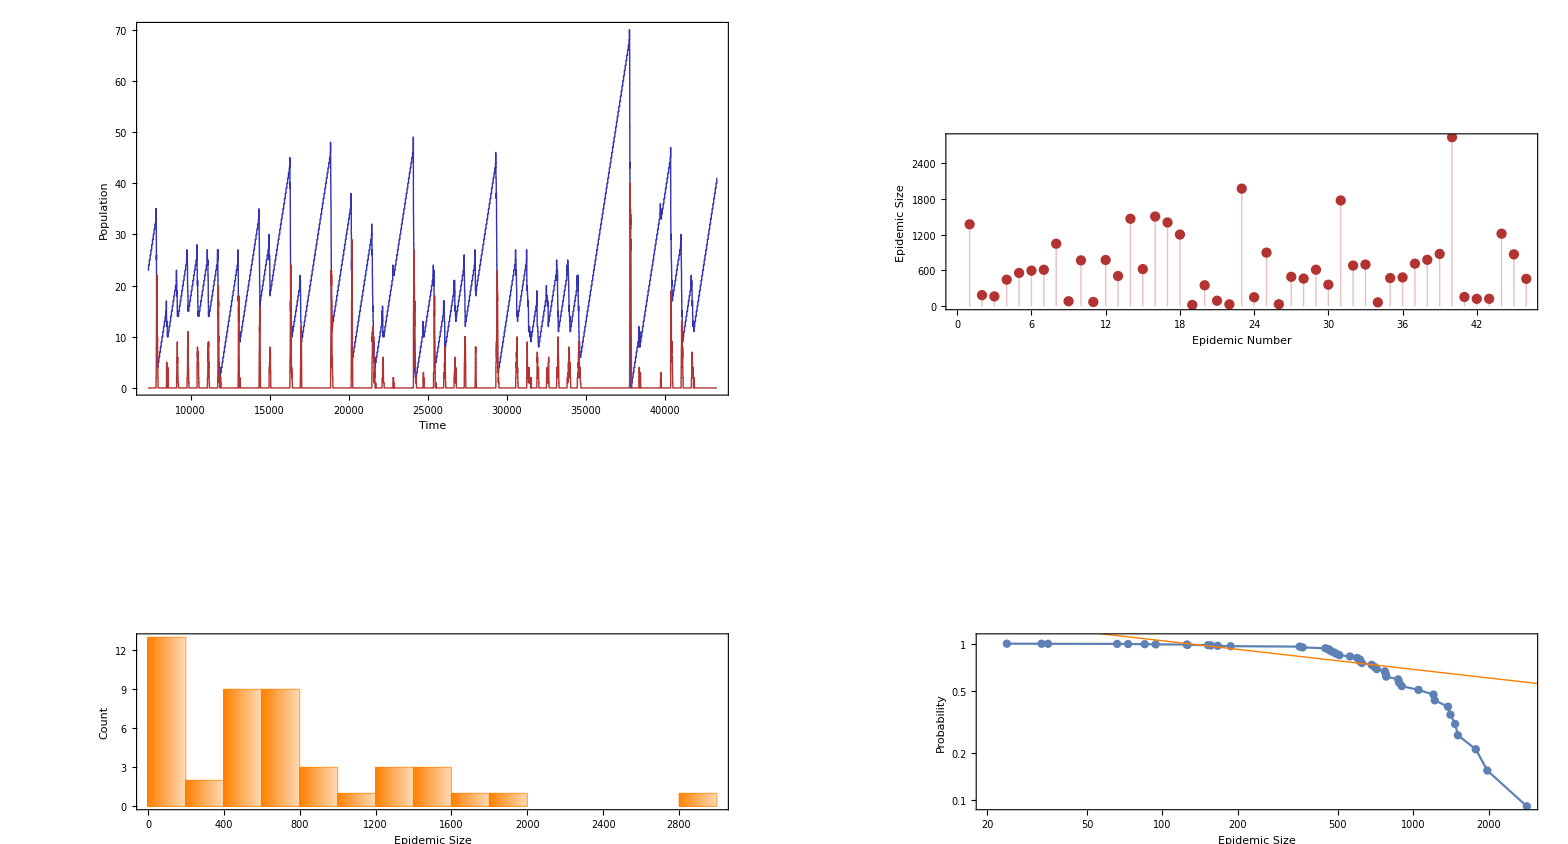

```mathematica
p=PopulationDataPlot[Table[Thread[{HistoryData[[7300;;-1,2]],HistoryData[[7300;;-1,i]]}],{i,{3,5}}]];
i=res["Epidemic Data"];
h=res["Histogram"];
l=Show[{res["Log Probability Distribution"],res["Linear Model"]}];
GraphicsGrid[{{p,i},{h,l}},ImageSize->{2500,Automatic}]
```

## Multiple Error Trend

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
xticks =Map[Style[#,FontSize->18]&, {"Stage 1", "Stage 2", "Stage 3", "Stage 4","Stage 5","Stage 6"}];
```

```mathematica
dbs0 = {"sim_v2_1_5_2017","sim_v5_1_5_2017","sim_v9_1_5_2017","sim_v13_1_6_2017","sim_v17_1_7_2017","sim_v25_1_9_2017"};
dbs1 = {"sim_v2_1_5_2017","sim_v6_1_5_2017","sim_v10_1_6_2017","sim_v24_1_8_2017","sim_v18_1_7_2017","sim_v23_1_8_2017"};
```

```mathematica
ress0=getLogData/@dbs0;
err0 =ress0[[#]]["R^2 Value"]&/@Range[Length[dbs0]];
```

```mathematica
ress1=getLogData/@dbs1;
err1 =ress1[[#]]["R^2 Value"]&/@Range[Length[dbs1]];
```

```mathematica
data = (MapThread[{Mean[{#1,#2}],StandardDeviation[{#1,#2}]/2}&,{err0,err1}]/.{{a_,b_/;b<0.01}:> {a,b+RandomReal[{0.01,0.015}]}})
```

{{0.663803,0.0111791},{0.683149,0.0134248},{0.780916,0.0199273},{0.893064,0.0221334},{0.942931,0.0177087},{0.943464,0.0201661}}

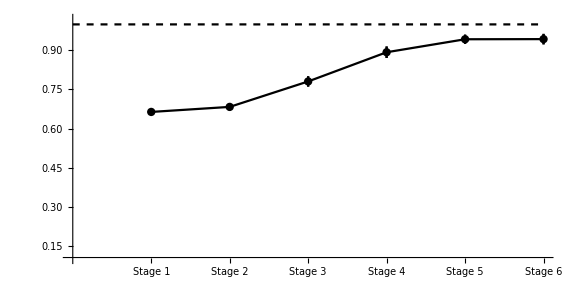
-Graphics-Correlation Coefficient

```mathematica
errImage=Labeled[
Show[{
ErrorListPlot[data,
Joined->True,PlotRange->{Automatic,{0.1,1.02}},Ticks->{Thread[{Range[Length[dbs1]],Rotate[#,Pi/3]&/@xticks}],Automatic},
Mesh->Full,PlotStyle->{Black,Thick}(*,AxesLabel->{Style["Increasing Complexity",Large],Style["Correlation Coefficient",Large]}*)],
Plot[1,{x,0,6},PlotStyle->{Black,Thick,Dashed}]
},AspectRatio->0.5,ImageSize->Large],
Rotate[Style["Correlation Coefficient",FontColor->Gray,FontSize->Large,FontWeight->Bold,FontFamily->"Helvetica"],Pi/2],Left]
```

Export["/Users/sahand/Research/paper1/SOC-SIR/images/Variation_Sweep.jpg", errImage]

"/Users/sahand/Research/paper1/SOC-SIR/images/Variation_Sweep.jpg"

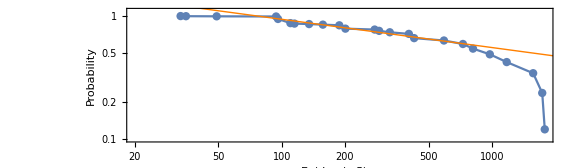

```mathematica
powerlaw=Show[ress1[[6]][#]&/@{"Log Probability Distribution","Linear Model"}]
```

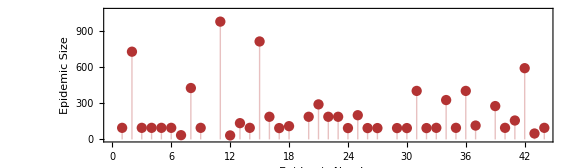

```mathematica
epidemic=Show[ress1[[6]][#]&/@{"Epidemic Data"}]
```

Export["/Users/sahand/Research/paper1/SOC-SIR/images/PowerLaw.jpg", powerlaw]

Export["/Users/sahand/Research/paper1/SOC-SIR/images/EpidemicTimeHistory.jpg", epidemic]

```mathematica
Manipulate[Labeled[Show[ToExpression[res][[n]][#]&/@{"Log Probability Distribution","Linear Model"}],ToExpression[res][[n]]["R^2 Value"],Top],{n,1,6,1},{res,{"ress0","ress1"}}]
```

Part::partd: Part specification ress0⟦1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{ress0⟦1⟧[Log Probability Distribution],ress0⟦1⟧[Linear Model]}].

Part::partd: Part specification ress0⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ress0⟦1⟧[Log Probability Distribution],ress0⟦1⟧[Linear Model]}].

Part::partd: Part specification ress0⟦1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{ress0⟦1⟧[Log Probability Distribution],ress0⟦1⟧[Linear Model]}].

Part::partd: Part specification ress0⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Stages

```mathematica
dbs0 = {"sim_v1_1_5_2017","sim_v5_1_5_2017","sim_v9_1_5_2017","sim_v13_1_6_2017","sim_v18_1_7_2017","sim_v23_1_8_2017"};
dbs1 = {"sim_v2_1_5_2017","sim_v6_1_5_2017","sim_v10_1_6_2017","sim_v13_1_6_2017","sim_v17_1_7_2017","sim_v23_1_8_2017"};
```

```mathematica
ress0=getLogData[#,AxisRange->5000]&/@dbs0;
err0 =ress0[[#]]["R^2 Value"]&/@Range[Length[dbs0]];
```

```mathematica
ress1=getLogData[#,AxisRange->5000]&/@dbs1;
err1 =ress1[[#]]["R^2 Value"]&/@Range[Length[dbs1]];
```

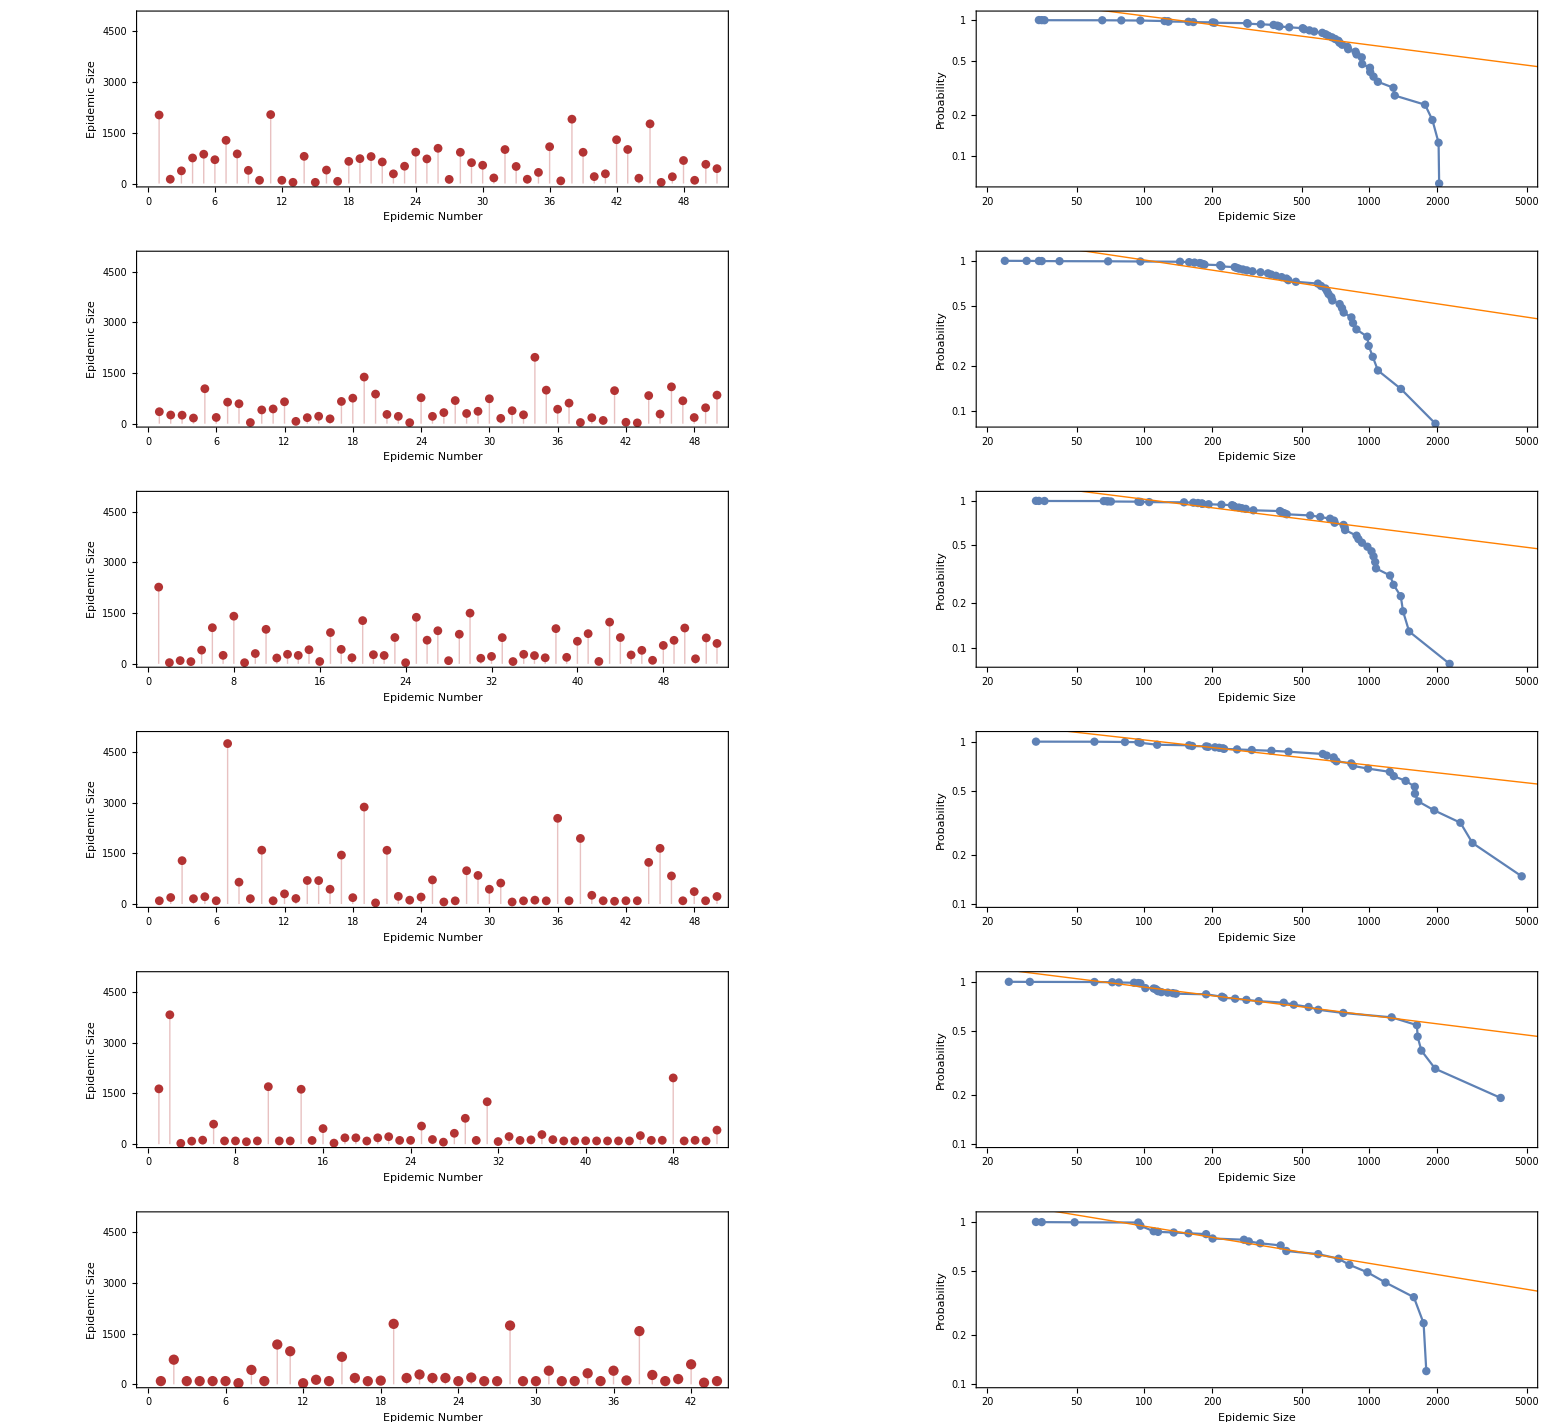

```mathematica
GraphicsGrid[
Map[
{#["Epidemic Data"],Show[{#["Log Probability Distribution"],#["Linear Model"]}]}
&,ress1],ImageSize->{2500,Automatic}
]
```

plots = Map[
   GraphicsRow[{#["Epidemic Data"], Show[{#["Log Probability Distribution"], #["Linear Model"]}]}, ImageSize -> {2500, Automatic}]
    &, ress0];

MapIndexed[Export["/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_" <> ToString[#2[[1]]] <> ".jpg", #1] &, plots]

{"/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_1.jpg", "/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_2.jpg", "/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_3.jpg", "/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_4.jpg", "/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_5.jpg", "/Users/sahand/Research/paper_ABM_SIR/SOC-SIR/images/revision2/stage_6.jpg"}

## Individual Data

```mathematica
db="sim_v1_11_14_2016";
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/"<>db],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
pid = 3;
```

```mathematica
pid=78;
```

```mathematica
getPerson[{pid},{"SusCells","InfCells","VirLoads"},3050,3150];
```

SELECT PersonID, Time, SusCells, InfCells, VirLoads FROM PersonValues where (PersonID=78) and (Time > 3050 and Time < 3150)

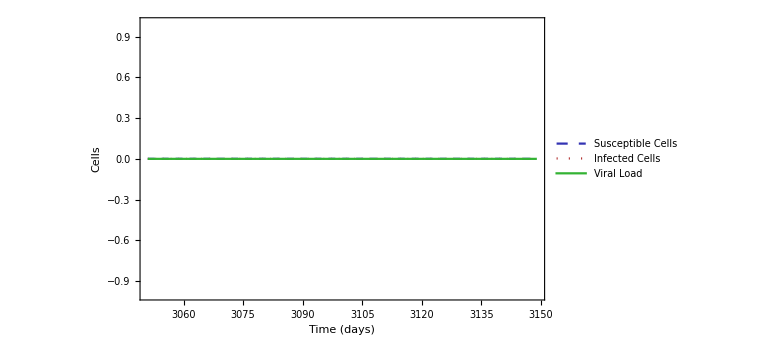

```mathematica
ihd=CellDataPlot[extractPerson[pid,{"SusCells","InfCells","VirLoads"}]]
```

Export["/Users/sahand/Research/paper1/SOC-SIR/images/IHD.jpg", ihd, "jpeg"];

## Contact Network

### Connecting to Database

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v24_1_8_2017"],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
allData=getConnections[conn];
```

```mathematica
data=DeleteDuplicates[Map[{#[[1,1,1]],#[[1,1,2]],Total[#[[All,-1]]]}&,GatherBy[Join[allData/.{{a_,b_,c_}:>{{a,b},c}},allData/.{{a_,b_,c_}:>{{b,a},c}}],First]]];
```

```mathematica
dd=Join[allData/.{{a_,b_,c_}:>{a,b,c}},allData/.{{a_,b_,c_}:>{b,a,c}}];
```

```mathematica
finalData=Join[Complement[Tuples[Range[120],2],data[[All,1;;2]]]/.{{a_,b_}:>{a,b,0}},data];
```

```mathematica
m = Max[finalData[[All,-1]]];
```

```mathematica
diag=False;
```

```mathematica
finalData = If[diag,finalData /. {{a_, b_, c_} :> If[a == b, {a, b, Max[Cases[finalData,{a,_,_}][[All,3]]]}, {a, b, c}]},finalData];
```

```mathematica
scaledData = finalData/.{{a_,b_,c_}:>{a,b,c/m}};
```

```mathematica
conNet=ListDensityPlot[dd,PlotLegends->False,ImageSize->Large,PlotRange->{{0,80},{0,80},All},ColorFunction->(RGBColor[#,#,#]&),ColorFunctionScaling->True,PlotTheme->"Business",InterpolationOrder->1,FrameLabel->{Style["Age",22],Style["Age",22]}]
```

Export["/Users/sahand/Research/paper1/SOC-SIR/images/contactnetwork.jpg", conNet, "jpeg"];

## Network

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v1_10_31_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
getGraph[{1,2,3}]
```

$Aborted[]

```mathematica
N@GlobalClusteringCoefficient[getGraph[Range[1000]]]
```

0.986953

```mathematica
N@GlobalClusteringCoefficient[getGraph[Range[1000]]]
```

0.986953

```mathematica
N@MeanClusteringCoefficient[getGraph[Range[1000]]]
```

0.991386

```mathematica
N@MeanClusteringCoefficient[getGraph[Range[1000]]]
```

0.987345

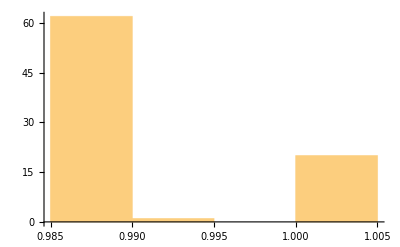

```mathematica
Histogram[N@LocalClusteringCoefficient[getGraph[Range[1000]]]]
```

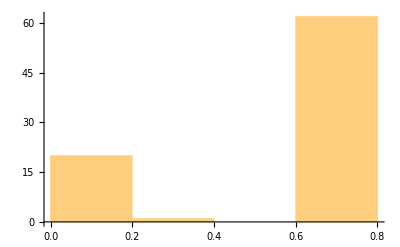

```mathematica
Histogram[BetweennessCentrality[getGraph[Range[1000]]]]
```

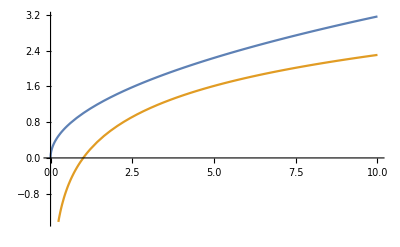

```mathematica
Plot[{Sqrt[x], Log[x]},{x,0,10}]
```